```mathematica
<< "/home/pablo/Escritorio/Uni/RRT/RandomData.m";
RandomData[]
RandomExp[100]
```

0.773033

0.00143182

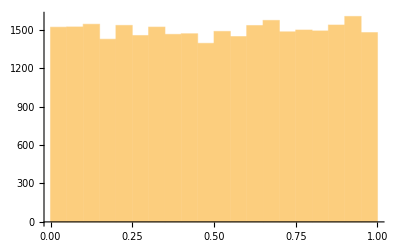

```mathematica
Histogram[Table[RandomData[],{30000}]]
```

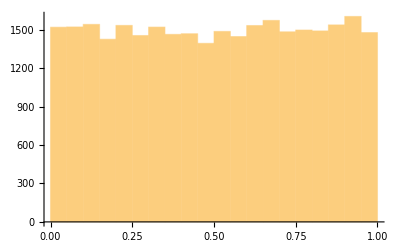

-Graphics-

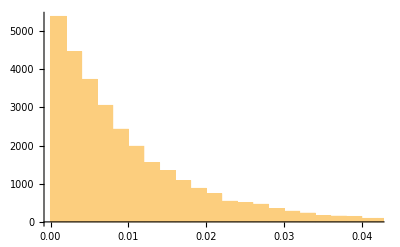

```mathematica
Histogram[Table[RandomExp[100],{30000}]]
```

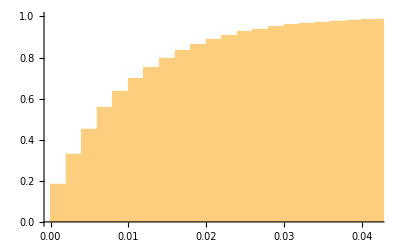

```mathematica
Histogram[Table[RandomExp[100],{30000}], 50,"CDF"]
```

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals]
```

```mathematica
nmax=1000;
mu=200;
ro=0.8;
lambda=mu*ro;
InterArrivalsTime=Table[RandomExp[lambda],{nmax}];
ArrivalsTime=Accumulate[InterArrivalsTime];
ServiceTime=Table[RandomExp[mu],{nmax}];
DepartureTime=FifoSchedulling[ArrivalsTime, ServiceTime];
```

```mathematica
ListPlot[{ArrivalsTime,DepartureTime}]
```

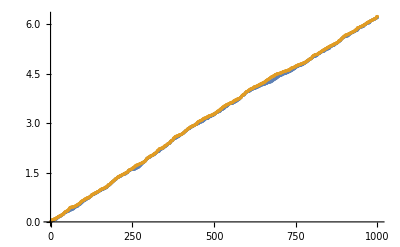

-Graphics-

```mathematica
Manipulate[ListPlot[{ArrivalsTime[[origin;;origin+width]],DepartureTime[[origin;;origin+width]]}],{origin,1,1000-width,1},{width,10,40,1}]
```

```mathematica
PointStair[lst_]:=
Module[
{n=0,lastTime=0},
Flatten[Map[({{lastTime,n},{lastTime=#,n++}})&,lst],1]
]
```

```mathematica
Manipulate[
ListLinePlot[{PointStair[ArrivalsTime[[1;;width]]],PointStair[DepartureTime[[1;;width]]]}],{width,10,40,1}]
```

```mathematica
ArrivalsEvent[lst_]:=Map[{#,1}&,lst]
DepartureEvent[lst_]:=Map[{#,-1}&,lst]
```

```mathematica
A=ArrivalsEvent[ArrivalsTime];
B=DepartureEvent[DepartureTime];

EventList=
Sort[Join[A,B]];
```

```mathematica
DrawMountain[lst_]:=Module[{n=0,lastTime=0},Flatten[Map[{{lastTime,n},{lastTime=#[[1]],If[#[[2]]==1,n++,n--]}}&,lst],1]]
listStat=DrawMountain[EventList];
Manipulate[ListLinePlot[listStat[[1;;width]]],{width,10,1000,1}]
```

```mathematica
GetProb[n_,lst_]:=
Module[{time=0,lastTime=0},Map[(If[#[[2]]==n,time+=#[[1]]-lastTime];
lastTime=#[[1]])&,lst];
time/Last[lst][[1]]]
```

```mathematica
GetProb[0,listStat]+GetProb[1,listStat]+GetProb[2,listStat]+GetProb[3,listStat]+GetProb[4,listStat]+GetProb[5,listStat]+GetProb[6,listStat]+GetProb[7,listStat]
```

0.998754